WolframAlphaQueryParseResults

```mathematica
Entity["Country","Chile"]["PopulationDensity"]
```

24.2824 people/km^2

```mathematica
Entity["Person","NikolaTesla::c4223"]["Properties"]
```

{other names,astrological sign,date of birth,place of birth,brothers,children,Chinese zodiac sign,daughters,date of death,place of death,father,full name,gender,height,husbands,image,space missions,mathematical contributions,mother,notable film appearances,notable film direction credits,notable film production credits,notable film writing credits,name,nationality,net worth,notable artworks,astronomical discoveries,notable books,famous chemistry problems,notable facts,notable inventions,physics contributions,occupation,parents,siblings,sisters,sons,spouses,weight,wives}

```mathematica
Entity["Person","NikolaTesla::c4223"]["Image"]
```

-Graphics-

```mathematica
Entity["Person","AlbertEinstein::6tb7g"]["Image"]
```

-Graphics-

```mathematica
Entity["FictionalCharacter","FrankensteinsMonster::7hsr6"]["Properties"]
```

{advertisement appearances,alter egos,alternate names,animation appearances,book appearances,cause of death,comic appearances,comic strip appearances,creator,date of birth,date of death,description,family relations,full name,gender,image,movie appearances,name,notable places,place of birth,place of death,play appearances,poem appearances,radio appearances,short name,short story appearances,song appearances,species,television appearances,video game appearances}

```mathematica
Entity["FictionalCharacter","FrankensteinsMonster::7hsr6"]["Creator"]
```

{{PeopleData,MaryShelley::7nf57}}

```mathematica
Entity["Country","Chile"]["BorderingCountries"]
```

{Argentina,Bolivia,Peru}

```mathematica
EntityValue["Planet","Image"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Problemas en Clase*)
(*Bandera De Suiza*)
Entity["Country","Switzerland"]["FlagImage"]
```

-Graphics-

```mathematica
Entity["Species","Species:LoxodontaAfricana"]["Image"]
```

-Graphics-

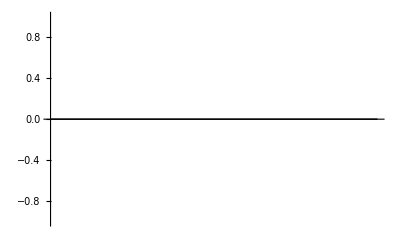

```mathematica
BarChart@EntityValue["Planet","Mass"]
```

```mathematica
ImageCollage[EntityValue["Planet","Image"]]
```

-Graphics-

```mathematica
EdgeDetect@EntityValue[Entity["Country","China"],"Flag"]
```

-Graphics-

```mathematica
EntityValue[Entity["Building","EmpireStateBuilding"],"Height"]
```

381. m

```mathematica
DominantColors[EntityValue[Entity["Artwork","TheStarryNight::VincentVanGogh"],"Image"]]
```

{RGBColor[0.2708752278513861, 0.3721256786182165, 0.5539685603708965],RGBColor[0.10682164139614381, 0.11661407877889521, 0.10438799333736279],RGBColor[0.4496934138322937, 0.5406536531765558, 0.5762096615622823],RGBColor[0.64821486872734, 0.6888255941422692, 0.6136113777213216],RGBColor[0.16759765802169313, 0.2298797507938432, 0.4896711728560374],RGBColor[0.6874844094094331, 0.6964444657151515, 0.46441315682118994],RGBColor[0.6926877578675958, 0.6283511391428719, 0.20568983971520127]}

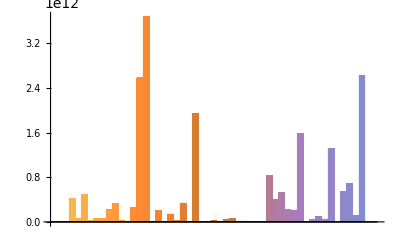

```mathematica
BarChart@List@EntityValue[Entity["GeographicRegion","Europe"]["Countries"],"GDP"]
```

```mathematica
ImageAdd[Entity["Species","Species:PhascolarctosCinereus"]["Image"],Entity["Country","Australia"]["FlagImage"]]
```

-Graphics-

```mathematica
(*Unidades*)
(*Se ingresan con Quantity[2.4, "Hours"], ctrl + =*)
Quantity[7.5, "Feet"]+Quantity[14, "Centimeters"]
```

242.6 cm

```mathematica
CurrencyConvert[100000 Quantity[, "ChileanPesos"],Quantity[, "USDollars"]]
```

FinancialData::notdate: Close is not a valid date range for FinancialData.

151.15 $

```mathematica
Quantity[0.3,"SpeedOfLight"]
```

0.3 c

```mathematica
UnitConvert[Quantity[0.3, "SpeedOfLight"],"Kilometers/Seconds"]
```

89937.7 km/s

```mathematica
Rotate[Entity["Person","AlbertEinstein::6tb7g"]["Image"],30°]
```

-Graphics-

```mathematica
Table[Rotate[Entity["Person","AlbertEinstein::6tb7g"]["Image"],n Degree],{n,0,360,30}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[Rotate[Entity["Person","AlbertEinstein::6tb7g"]["Image"],n Degree],{n,0,360,10}]
```

```mathematica
AnglePath[{30°,60°,90°}]
```

{{0,0},{(√3)/2,1/2},{(√3)/2,3/2},{-1+(√3)/2,3/2}}

```mathematica
Graphics@Line@%
```

-Graphics-

```mathematica
Manipulate[Graphics@Line@AnglePath@Table[n Degree,{n,m}],{m,1,720,10}]
```

```mathematica
(*Ejercicios*)
UnitConvert[4.5 Quantity[, "Pounds"],"Kilograms"]
```

2.04117 kg

```mathematica
UnitConvert[Quantity[60.25, ("Miles")/("Hours")],"Kilometers/Hours"]
```

96.963 km/h

```mathematica
Entity["Planet","Earth"]["Mass"]/EntityValue[Entity["PlanetaryMoon","Moon"],"Mass"]
```

81.3

```mathematica
EntityValue[Entity["Planet","Earth"],"Mass"]/EntityValue[Entity["PlanetaryMoon","Moon"],"Mass"]
```

81.3

```mathematica
DisFromEarth=
UnitConvert[EntityClass["Planet",All]["DistanceFromEarth"]
,"LightMinutes"]
```

{6.95916 light minutes,11.0256 light minutes,0. light minutes,17.3454 light minutes,40.0644 light minutes,83.3214 light minutes,173.22 light minutes,255.999 light minutes}

```mathematica
NamesPl = EntityClass["Planet",All]["Name"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
Riffle[NamesPl,DisFromEarth]
```

{Mercury,6.95916 light minutes,Venus,11.0256 light minutes,Earth,0. light minutes,Mars,17.3454 light minutes,Jupiter,40.0644 light minutes,Saturn,83.3214 light minutes,Uranus,173.22 light minutes,Neptune,255.999 light minutes}

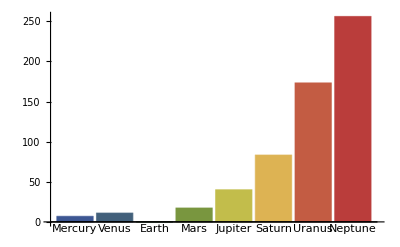

```mathematica
BarChart[DisFromEarth,ChartLabels->NamesPl,ChartStyle->"DarkRainbow"]
```

```mathematica
Table[Rotate[Alphabet[][[n]],RandomInteger[{0,360}] Degree],{n,Length[Alphabet[]]}]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Alphabet::noalpha: The alphabet 1 is not known or not available.

Alphabet[1]